# Задание 08.

## Двумерное случайное блуждание

## Мосейков Игнатий Геннадьевич, группа 21372

## Задача

В начальный момент времени частица оказывается в точке (0,0), двигаясь вдоль положительного направления оси x θ_0=0. 

Частица либо поглощается с вероятностью p (и на этом ее траектория обрывается), либо с вероятностью (1-p) рассеивается

Если происходит рассеяние то добавка к углу (относительно предыдущего направления) распределена согласно плотности распределния вероятности
p(θ)∝ cos^3 θ, -π/2≤θ≤π/2,
т.е. новое направление движения пересчитывается по формуле θ_(n+1)=θ_n+θ, 

Если частица рассеялась, то она перемещается на расстояние L вдоль нового направления движения, причем вероятность значения L определяется длиной свободного пробега λ
p(L) ∝ e^(-L/λ), L≥0

Применяется метод обратной функции распределения

все предварительные алгебраические символьные расчеты для метода обратной функции распределения (интегрирование плотности распределения, нормировка ее на единицу, решение уравнения для обратной функцией распределения) выполните в системе Wolfram Mathematica. Результатом вычислений должно быть явное выражение для L и θ через базовые случайные величины, распределенные от нуля до единицы. (Далее в качестве базового генератора случайных чисел можно использовать RandomReal[])

напишите генератор genL, который при каждом вызове возвращает случайное значения для расстояния, на которое перемещается частица, при заданном значении длины свободного пробега lambda. (параметр lambda можно принимать и сохранять в конструкторе init[genL, lambda])

```mathematica
createGenL[genL_, lambda_]:=(
genL[]:=Block[
{L,eq,res,normL},normL = Integrate[Exp[-t/lambda],{t,0,Infinity}];eq=Integrate[Exp[-t/lambda]/normL,{t,0,L}];res=Solve[eq==RandomReal[],L,InverseFunctions->True];First[L/.res]
];
);
```

```mathematica
createGenL[genL,0.5]
genL[]
```

0.101023

напишите генератор genTheta, который возвращает случайное изменение для угла рассеяния

```mathematica
createGenTheta[genTheta_]:=(
genTheta[]:=Block[
{theta,eq,res,normTheta},
normTheta = Integrate[Power[Cos[t],3],{t,-Pi/2,Pi/2}];
eq=Integrate[Power[Cos[t],3]/normTheta,{t,-Pi/2, theta}];
res=Solve[eq==RandomReal[],theta,InverseFunctions->True];
First[Select[theta/.res,Element[#,Reals]&&Abs[#]<Pi/2&]]
];
);
createGenTheta[genTheta]
genTheta[]
```

0.270875

Cгенерируйте достаточное количество случайных значений, постройте гистограммы для расстояний и углов, сравните с ожидаемыми плотностями распределений (Mathematica умеет рисовать нормированные гистограммы, см. справку Histogram)

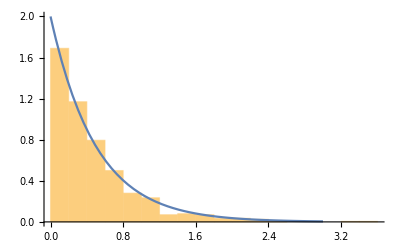

```mathematica
Show[Histogram[Table[genL[],{i,1000}],20,"PDF"],Plot[Evaluate[Exp[-t/0.5]/0.5],{t,0,3.0}]]
```

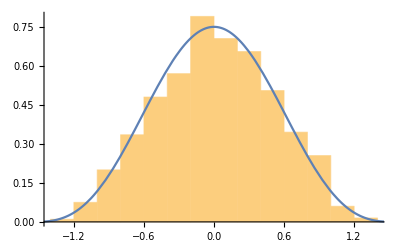

```mathematica
Show[Histogram[Table[genTheta[],{i,1000}],16,"PDF"],Plot[Evaluate[3*Power[Cos[t],3]/4],{t,-Pi/2,Pi/2}]]
```

Напишите функцию trajectory[p, genL, genTheta], которая принимает вероятность обрыва траектории и имена генераторов расстояния и угла рассеяния и возвращает траекторию движения частицы. В реализации также могут быть полезны инструменты для работы с повторяющимися применениями функций (Applying Functions Repeatedely)

```mathematica
trajectory[0.1,genL,genTheta] (* генератор genL использует lambda = 1.0 *)
```

{{0,0},{0.922611,0.},{2.38996,-2.40254},{2.60577,-2.60678},{2.94296,-2.79911},{2.96759,-2.82337},{3.20167,-2.92143},{3.45297,-2.99513}}

```mathematica
createGenL[genL,1.0];
trajectory[p_,genL_,genTheta_]:=Block[{path,bernulli,x,y,theta, gL, gTheta},
x=0;
y=0;
theta=0;
path={{0,0}};
bernulli=BernoulliDistribution[p];
While[RandomVariate[bernulli]==0,(
gL = genL[];
gTheta = genTheta[];
theta+=gTheta;
x+=gL*Cos[theta];
y+=gL*Sin[theta];
AppendTo[path,{x,y}];
)];
path
];
```

```mathematica
trajectory[0.1,genL,genTheta]
```

{{0,0},{0.31804,-0.103588},{0.853977,0.0416575},{0.895132,0.0701513},{0.82368,0.543523},{0.756331,0.863872},{0.437766,1.53457},{0.906525,3.10633},{1.008,3.23918},{1.17034,4.41749},{1.25379,4.47367},{1.32144,4.61573},{1.74594,6.04075},{2.50687,7.38755},{2.51804,7.46411},{2.79257,7.81602},{2.87182,7.9749},{3.52551,8.75134},{3.63276,8.82925},{6.56084,8.79625},{7.45873,9.00128},{7.89627,9.05336},{7.90725,9.04771},{8.18526,8.73762},{10.6038,8.16962}}

Нарисуйте несколько траекторий

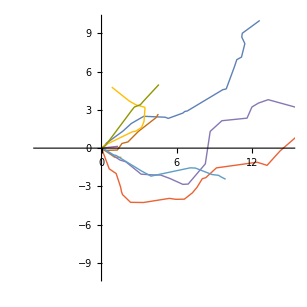

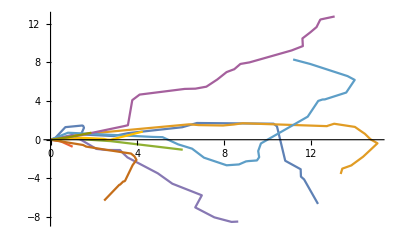

```mathematica
ListLinePlot[Table[trajectory[0.1,genL,genTheta],{i,10}]]
```

определите (численно) по набору траекторий среднее и дисперсию для глубины проникновения вдоль оси х

```mathematica
depths =Table[Last[trajectory[0.1,genL,genTheta]][[1]],{i,20}]
```

{0.0713106,4.44664,1.56339,1.30102,-0.134343,-0.0285919,5.71044,13.2338,13.2491,-1.27023,3.11318,1.96846,3.1408,3.3015,4.06545,11.4833,2.08869,0.756917,8.32753,7.72776}

```mathematica
Print[Mean[depths],"+-",StandardDeviation[depths]]
```

4.20581+-4.4235

Метод обратной функции распределения не удается применить для генерации θ ∝ cos^n(θ),θ∈[-π/2,π/2] при произвольной степени n≥0 (возникают спецфункции, которые не позволяют в явном виде выразить θ). Но можно, например, использовать метод исключения (метод Неймана). Реализуйте генератор на основе метода исключения. При нескольких значениях n, нарисуйте гистограммы и плотности распределений. Как изменяются траектории при увеличении степени n?

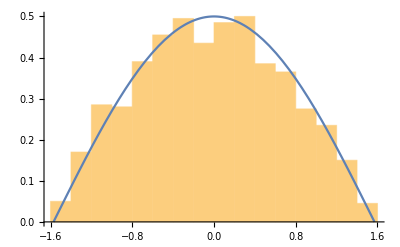

3.08638+-4.91772

```mathematica
createGenTheta[genTheta_,n_, a_,b_]:=(
genTheta[]:=Block[
{mu,r,M},
M=First[FindMaximum[Power[Cos[t],n],{t,a,b}]];
r=(b-a)*RandomReal[]+a;
mu=M*RandomReal[];
While[mu>Power[Cos[r],n],(
r=(b-a)*RandomReal[]+a;
mu=M*RandomReal[];
)];
r
];
);
n=1;
createGenTheta[genTheta,n,-Pi/2,Pi/2];
normTheta = Integrate[Power[Cos[t],n],{t,-Pi/2,Pi/2}];
Show[Histogram[Table[genTheta[],{i,1000}],16,"PDF"],Plot[Evaluate[Power[Cos[t],n]/normTheta],{t,-Pi/2,Pi/2}]]
depths =Table[Last[trajectory[0.1,genL,genTheta]][[1]],{i,20}];
Print[Mean[depths],"+-",StandardDeviation[depths]];
```

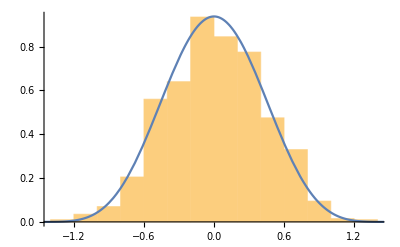

4.78866+-5.17324

```mathematica
n=5;
createGenTheta[genTheta,n,-Pi/2,Pi/2];
normTheta = Integrate[Power[Cos[t],n],{t,-Pi/2,Pi/2}];
Show[Histogram[Table[genTheta[],{i,1000}],16,"PDF"],Plot[Evaluate[Power[Cos[t],n]/normTheta],{t,-Pi/2,Pi/2}]]
depths =Table[Last[trajectory[0.1,genL,genTheta]][[1]],{i,20}];
Print[Mean[depths],"+-",StandardDeviation[depths]];
```

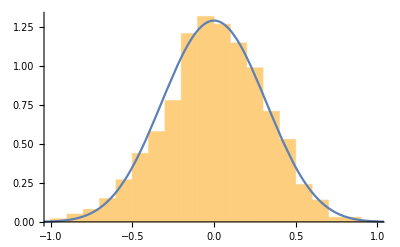

5.92704+-6.06908

```mathematica
n=10;
createGenTheta[genTheta,n,-Pi/2,Pi/2];
normTheta = Integrate[Power[Cos[t],n],{t,-Pi/2,Pi/2}];
Show[Histogram[Table[genTheta[],{i,1000}],16,"PDF"],Plot[Evaluate[Power[Cos[t],n]/normTheta],{t,-Pi/2,Pi/2}]]
depths =Table[Last[trajectory[0.1,genL,genTheta]][[1]],{i,20}];
Print[Mean[depths],"+-",StandardDeviation[depths]];
```

Как изменяются траектории при увеличении степени n -> частицы пролетают большее растояние